```mathematica
Clear["Global`*"] 
x=.;y=.;r=.; 
L=100;
psi = Pi/2;
a= 10;
b = 10;
c= 10;
r[x_,y_]:={((L/(2psi) )+a  Cos[y])Cos[x], ((L/(2psi) )+b Cos[y] )Sin[x], c Sin[y]};

gx[x_,y_]=Simplify[D[r[x,y],x]];
gy[x_,y_]=Simplify[D[r[x,y],y]];

gxx[x_,y_]:=gx[x,y].gx[x,y];
hx[x_,y_]:=Sqrt[gxx[x,y]];

gyy[x_,y_]:=gy[x,y].gy[x,y];
hy[x_,y_]:=Sqrt[gyy[x,y]];
nx[x_,y_]:=gx[x,y]/hx[x,y];
ny[x_,y_]:=gy[x,y]/hy[x,y];
nz[x_,y_]:=Cross[nx[x,y],ny[x,y]];

tamanho=0.3;

arrow[center_,direc_,color_,size_]:=Module[{dir},dir=Sqrt[3] direc/Sqrt[direc.direc];
Show[Graphics3D[{color,Specularity[Black,20000],EdgeForm[None],Cylinder[{center-tamanho  dir,center+size dir},tamanho/2],Cone[{center+size dir,center+(size+2tamanho) dir},tamanho],Sphere[center,0]},Lighting->"Neutral"]]];
arrowp[center_,direc_,color_]:=Module[{dir},dir=direc;
Show[Graphics3D[{color,Specularity[Black,20000],EdgeForm[None],Cylinder[{center-dir,center+dir},1/3],Cone[{center+2dir,center+2 dir},1.],Sphere[center-dir,0.]},Lighting->"Neutral"]]]
```

```mathematica
x0=-psi/2.2;
y0=Pi/2.5;

ϕ[x_,y_]:=If[x==0 && y==Pi/2,0,ArcTan[hx[x,y]*(x-x0),hy[x,y](y-y0)] +Pi/2];

nzz[x_,y_]:=nz[x,y];

θ[x_,y_]:=2ArcTan[(5Exp[1.52(5-Sqrt[(hx[x,y]^2(x-x0)^2)+(hy[x,y]^2(y-y0)^2)])/8.43])/(Sqrt[(hx[x,y]^2(x-x0)^2)+(hy[x,y]^2(y-y0)^2)])]


mx[x_,y_]:=Sin[θ[x,y]]*Cos[ϕ[x,y]]*nx[x,y];
my[x_,y_]:=Sin[θ[x,y]]*Sin[ϕ[x,y]]*ny[x,y];
mz[x_,y_]:=Cos[θ[x,y]]*nz[x,y];
mt[x_,y_]:=mx[x,y]+my[x,y]+mz[x,y];
```

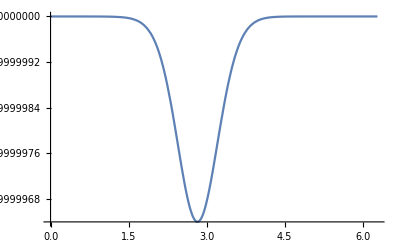

```mathematica
Plot[Cos[θ[psi/2,y]],{y,0,2Pi},PlotRange->Full]
```

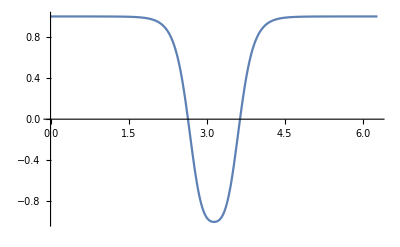

-Graphics-

```mathematica
Figura=ParametricPlot3D[r[x,y],{x,-psi,psi},{y,0,2Pi},Mesh->None,Axes->True,PlotPoints->50,Boxed->False,ColorFunction->(Blue&),ColorFunctionScaling->False];

Figura=ParametricPlot3D[r[u,v],{u,-psi,psi},{v,0,2Pi},Mesh->None,Axes->False,PlotPoints->100,Boxed->False,ColorFunction->Function[{x,y,z,u,v},ColorData[{"MintColors",{-1.0,1.0}}][Cos[θ[u,v]]]],ColorFunctionScaling->False];



dibujo1=Flatten[Table[arrow[r[x,y],mt[x,y],RGBColor[1.0,0.7,0],tamanho],{x,-psi,psi,0.07},{y,0,2Pi,0.2}],1];

Show[Figura,dibujo1]
```

-Graphics3D-

```mathematica
Show[%884,ViewPoint->Above]
```